# Vaje iz Mathematice, 1. del

### 1. naloga:

Izračunaj vrednost izraza  ((20+316)^7-55)/(33·12)^3

Izračunaj še numerično vrednost istega izraza na 20 mest natančno.

```mathematica
((20+316)^7 -55)/(33*12)^3
```

483476023799709641/62099136

```mathematica
N[((20+316)^7 -55)/(33*12)^3,20]
```

7.7855515381036805568×10^9

### 2. naloga:

Poenostavi izraz  2^x+5a 2^x+2^(x+2)

```mathematica
Simplify[2^x + 5a 2^x +2^(x+2)]
```

5 2^x (1+a)

### 3. naloga:

Poišči največji skupni delitelj števil 536, 1248, 2320.

Poišči še najmanjši skupni večkrat teh števil.

```mathematica
GCD[536,1248,2320]
```

8

```mathematica
LCM[536,1248,2320]
```

12124320

### 4. naloga:

Seštej vsa soda števila na intervalu [1,100].

```mathematica
Sum[x,{x,2,100,2}]
```

2550

### 5. naloga:

Izračunaj  ∑_(k=1)^∞ (k^2+1)/k^4

```mathematica
Sum[(k^2+1)/(k^4),{k,1,Infinity}]
```

1/90 π^2 (15+π^2)

### 6. naloga:

Izračunaj vrednost izraza (sin α + sin β)/(cos^2(α - β) - sin^2(β-α)) za kota α=1830°  in  β=270°.

```mathematica
(Sin[α]+Sin[β])/(Cos[α-β]^2-Sin[β-α]^2) /. {α -> 1830Degree,β-> 270Degree}
```

1

### 7. naloga:

Izračunaj vrednost izraza  (x^5-2 x^2+3x+4)/(x^5-2x-1)  pri x=1, 2, ..., 10. 
Uporabi transformacijsko pravilo in ukaz  ReplaceAll  oz.  /.

Isto nalogo reši še s pomočjo ukaza Table.

```mathematica
(x^5-2x^2+3x+4)/(x^5-2x-1)/.x-> {1,2,3,4,5,6,7,8,9,10}
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
(x^5-2x^2+3x+4)/(x^5-2x-1)/.x-> Table[i,{i,10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

### 8. naloga:

Dan je pravilen šestkotnik s stranico r. Kolikšna je ploščina kolobarja, ki ga določata včrtana in očrtana krožnica?

```mathematica
PloscinaKolobarjaSestkotnik[r_]:=Module[{visinaTrikotnika,ploscinaOcrtanega,ploscinaVcrtanega},
visinaTrikotnika= Sqrt[r^2-r/2];
ploscinaOcrtanega = Pi *r^2;
ploscinaVcrtanega = Pi *visinaTrikotnika^2;
ploscinaOcrtanega - ploscinaVcrtanega
]
```

```mathematica
PloscinaKolobarjaSestkotnik[3]
```

(3 π)/2

### 9. naloga:

Sin je 3 leta starejši od hčere, mati pa je 23 let starejša od sina. Pred 6 leti je imela mati 4 krat toliko let kot sin in hči skupaj. Koliko je star vsak od njih?

```mathematica
Solve[{sin == hci+3,mati ==sin+23,mati-6==4*(sin-6+hci-6) },{sin,hci,mati}]//First
```

{sin→11,hci→8,mati→34}

### 10. naloga:

Poišči vsa kompleksna števila, ki zadoščajo enačbi  z̄=z^2

```mathematica
Solve[Conjugate[z] == z^2]
```

{{z→0},{z→1},{z→-1/2-(ⅈ √3)/2},{z→-1/2+(ⅈ √3)/2}}

### 11. naloga:

Koliko začetnih členov zaporedja s splošnim členom  a_n=16-2n  moramo sešteti, da bo vsota enaka 36?

```mathematica
Solve[Sum[16 - 2n,{n,1,x}]== 36,x]
```

{{x→3},{x→12}}

```mathematica
Sum[16 - 2n,{n,1,12}]
```

36

### 12. naloga:

Dokaži, da je x=1 rešitev enačbe  a x^2-2b x+c=0, če a, b in c sestavljajo aritmetično zaporedje.

```mathematica
Solve[a x^2 - 2 b x+ c== 0/. {b -> a+d,c-> a +2d},x]
```

{{x→1},{x→(a+2 d)/a}}

### 13. naloga:

Določi vrednost parametra a v enačbi (2a x+3a)/(3a + 5x)=(3a-4)/(3a + 5x), da bo  x=2  rešitev enačbe.

```mathematica
Solve[(2 a x+3a)/(3a+5x)== (3a -4)/(3a+5x)/.x -> 2,a]//First
```

{a→-1}

### 14. naloga:

Na kakšne načine lahko plačamo poštnino 2,27 EUR z znamkami za 10, 23 in 37 centov?

```mathematica
Solve[{10x+23y+37z == 227,{x,y,z} ≥ 0},Integers]
```

{{x→1,y→3,z→4},{x→2,y→9,z→0},{x→7,y→2,z→3},{x→13,y→1,z→2},{x→19,y→0,z→1}}

### 15. naloga:

Poišči štirimestno število, ki je popoln kvadrat in katerega prvi dve števki sta med seboj enaki, drugi dve pa prav tako med seboj enaki.

```mathematica
Solve[{Sqrt[1100x+11y]== z,z ≥ 1,1≤ {x,y} ≤ 9},Integers]
```

{{x→7,y→4,z→88}}

### 16. naloga:

Na kocko s stranico a postavimo drugo kocko s telesno diagonalo, enako stranici prve kocke, na drugo kocko spet tretjo s telesno diagonalo, enako stranici druge kocke, in to ponavljamo brez konca. Izračunaj višino tako dobljenega telesa.

Izračunaj še prostornino tako dobljenega telesa.

```mathematica
Sum[a/Sqrt[3]^i,{i,0,Infinity}]
```

-(3 a)/(-3+√3)

```mathematica
Sum[(a/Sqrt[3]^i)^3,{i,0,Infinity}]
```

-(9 a^3)/(-9+√3)

### 17. naloga:

Določi premico y=k x+n, ki gre skozi točki (-2,3) in (6,-1).

Nariši dobljeno premico na intervalu [-3,7] tako, da bosta enoti na koordinatnih oseh enako veliki.
Na sliki označi še točki, skozi kateri poteka premica.

```mathematica
tocka1={-2,3}
tocka2 ={6,-1}
```

{-2,3}

{6,-1}

```mathematica
k =(tocka2-tocka1)[[2]]/(tocka2-tocka1)[[1]]
```

-1/2

```mathematica
n = a/.First[Solve[y==k x + a/.{x -> tocka1[[1]],y -> tocka1[[2]]},a ]]
```

2

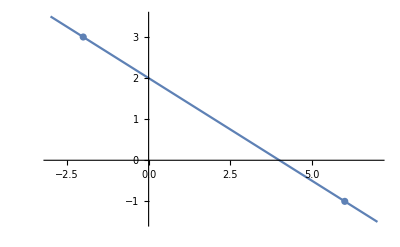

```mathematica
Show[Plot[{k x+n},{x,-3,7}],ListPlot[{tocka1,tocka2}]]
```

### 18. naloga:

Določi inverzno funkcijo funkcije  y=2ln(3x-1)

Nariši grafa obeh funkcij v istem koordinatnem sistemu.

```mathematica
osnovna = 2 Log[3x -1 ]
```

2 Log[-1+3 x]

```mathematica
inverzna =First[y/.Solve[x == 2Log[3y-1],y]][[1]]
```

1/3 (1+ⅇ^(x/2))

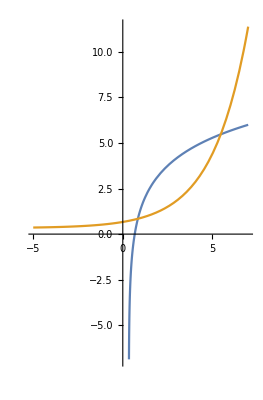

```mathematica
Plot[{osnovna,inverzna},{x,-5,7},AspectRatio->Automatic]
```